```mathematica
CreateDatabaseFromYahooFile[path_]:=Block[{dataset,dates,prices},
dataset = Import[path];
dates = Map[DateObject,Drop[dataset[[All,1]],1]];
prices = Drop[dataset[[All,5]],1];
Transpose[{dates,prices}]
];
```

```mathematica
files = FileNames["*",FileNameJoin[{NotebookDirectory[],"BMV"}]];
```

```mathematica
stocks = Map[FileBaseName,files];
```

```mathematica
stocks
```

{AC.MX,ALPEKA.MX,ALSEA.MX,AMXL.MX,ASURB.MX,BBAJIOO.MX,BIMBOA.MX,BOLSAA.MX,BSMXB.MX,CEMEXCPO.MX,CUERVO.MX,GAPB.MX,GCARSOA1.MX,GCC.MX,GENTERA.MX,GFNORTEO.MX,GMEXICOB.MX,GRUMAB.MX,IENOVA.MX,KIMBERA.MX,KOF,LABB.MX,LIVEPOLC-1.MX,MEGACPO.MX,MXCHF,OMAB.MX,PE&OLES.MX,PINFRA.MX,RA.MX,TLEVISACPO.MX}

```mathematica
Needs["AdvancedMapping`"];
```

```mathematica
dataset = ProgressParallelMap[CreateDatabaseFromYahooFile,files];
```

```mathematica
availableDates = Sort@DeleteDuplicates[Flatten[dataset[[All,All,1]]]];
```

```mathematica
availableDates
```

{Day: Tue 14 Sep 1993,Day: Wed 15 Sep 1993,Day: Thu 16 Sep 1993,Day: Fri 17 Sep 1993,Day: Mon 20 Sep 1993,Day: Tue 21 Sep 1993,Day: Wed 22 Sep 1993,Day: Thu 23 Sep 1993,Day: Fri 24 Sep 1993,6760,Day: Mon 23 Dec 2019,Day: Tue 24 Dec 2019,Day: Thu 26 Dec 2019,Day: Fri 27 Dec 2019,Day: Mon 30 Dec 2019,Day: Tue 31 Dec 2019,Day: Thu 2 Jan 2020,Day: Fri 3 Jan 2020,Day: Mon 6 Jan 2020}
 |  |  |  |

```mathematica
DateObject[{2002,11,20},"Day","Gregorian",-6.]
```

```mathematica
GetPriceAtDate[dataset_,date_]:=Block[{pos},
pos = FirstPosition[dataset,{date,_}];
If[pos =!=Missing["NotFound"],Last[Extract[dataset,pos]],None]
];
GetPricesFromDatasetAtDate[dataset_,date_]:=Table[GetPriceAtDate[currentDataset,date],{currentDataset,dataset}];
```

```mathematica
GetPricesFromDatasetAtDate[dataset,DateObject[{2002,11,20},"Day","Gregorian",-6.]]
```

{16.,None,1.92373,1.09833,9.92,None,3.6725,None,None,7.12811,None,None,3.96337,7.2,None,4.85,3.36748,9.76523,None,7.67,22.19,None,10.7,None,None,None,16.85,1.1,None,13.48}

```mathematica
datedDatabase =ProgressParallelMap[{#,GetPricesFromDatasetAtDate[dataset,#]}&,availableDates,Method->"CoarsestGrained"];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"BMV_Raw.mx"}],datedDatabase]
```

/home/carlos/Documentos/Maestria/Econofisica/Datos/BMV_Raw.mx

```mathematica
FormatPrices[prices_]:=Block[{propagateBackwards,propagateForward},
propagateBackwards = FixedPoint[
SequenceReplace[#,
{
{"null",x_ /;NumberQ[x]}:>Sequence[x,x],
{None,x_ /;NumberQ[x]}:>Sequence[x,x]
}
]&,
prices
];
propagateForward = FixedPoint[
SequenceReplace[#,
{
{x_ /;NumberQ[x],"null"}:>Sequence[x,x],
{x_ /;NumberQ[x],None}:>Sequence[x,x]
}
]&,
propagateBackwards
];
Return[propagateForward];
];
```

```mathematica
Returns[prices_, lag_:1]:= Round[N[Drop[prices,lag]/Drop[prices,-lag]-1],0.000001];
```

```mathematica
DiscretizeReturns[returns_]:=Block[{quantiles,intervals,rules},
quantiles = Quantile[DeleteCases[returns,0.0],{1/3,2/3}];
intervals = Map[Interval,Partition[Join[{-∞},quantiles,{∞}],2,1]];
rules = {
(x_ /;IntervalMemberQ[intervals[[1]],x])->-1,
(x_ /;IntervalMemberQ[intervals[[2]],x])->0,
(x_ /;IntervalMemberQ[intervals[[3]],x])->1
};
ReplaceAll[returns,rules]
];
```

```mathematica
stocks = Transpose@datedDatabase[[All,2]];
```

```mathematica
processed = ProgressMap[FormatPrices,stocks];
```

```mathematica
returns = Map[Returns,processed];
```

```mathematica
discretized = Map[DiscretizeReturns,returns];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"bmv.csv"}],Transpose[discretized]]
```

/home/carlos/Documentos/Maestria/Econofisica/Datos/bmv.csv

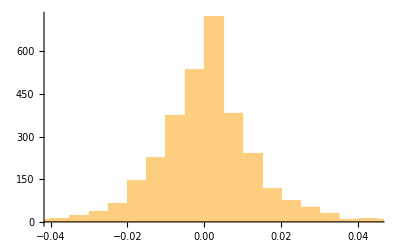

```mathematica
Histogram@DeleteCases[returns[[1]],0.0]
```

```mathematica
datedDatabase[[All,2]][[1;;2]]
```

{{None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,7.41667,None,None,None,None,None,None,None,None,None},{None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,None,7.33333,None,None,None,None,None,None,None,None,None}}

```mathematica
Transpose@Transpose[processed][[1;;3]]
```

{{16.,16.,16.},{27.95,27.95,27.95},{2.89777,2.89777,2.89777},{2.18133,2.18133,2.18133},{12.8,12.8,12.8},{30.14,30.14,30.14},{5.025,5.025,5.025},{16.49,16.49,16.49},{29.98,29.98,29.98},{8.7897,8.7897,8.7897},{35.43,35.43,35.43},{30.2,30.2,30.2},{6.43722,6.43722,6.43722},{7.,7.,7.},{26.49,26.49,26.49},{3.535,3.535,3.535},{4.81591,4.81591,4.81591},{9.17251,9.17251,9.17251},{38.66,38.66,38.66},{12.3,12.3,12.3},{7.41667,7.33333,7.33333},{8.335,8.335,8.335},{18.4,18.4,18.4},{37.,37.,37.},{3.77,3.77,3.77},{29.44,29.44,29.44},{25.,25.,25.},{2.02,2.02,2.02},{32.07,32.07,32.07},{33.1,33.1,33.1}}

```mathematica
Map[Returns,Transpose@Transpose[processed][[1;;3]]]
```

{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{-0.011236,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.}}

```mathematica
Round
```

```mathematica
Transpose[returns][[1;;10]]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.011236,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.017045,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00578,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.017241,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.011696,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.028902,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.022472,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.005495,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.016393,0.,0.,0.,0.,0.,0.,0.,0.,0.}}